## Constants & Preliminaries

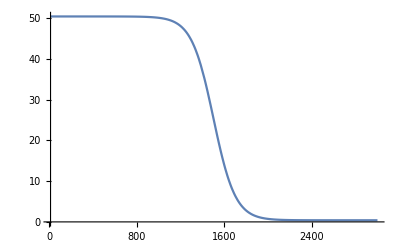

```mathematica
(*Needs["RootSearch`"]*)

fullSimplifyReal[x_]:=Assuming[_Symbol ∈ Reals, FullSimplify@x]

myFormatConvertToNegativePowers = StandardForm[#/.Power[expr_, r_?Negative] :> Superscript[expr,r] ]&;

CL=2.997925 10^10;
Gr=6.67 10^-8;
ARAD=7.56464 10^(-15);

KPE=0.4;
KPDUST = 50;       (* dust kappa *)


SGT=6.6524 10^-25; (*Thomson cross section cm^2*)
RGAS=8.31 10^7/μm/.μm->1.;
KB=1.38062 10^-16;
PC=3.085678 10^18;
Msol=1.989 10^33;

MBH=10^7 Msol;

MP=1.672661 10^-24;

SGB = ARAD*CL/4;
DAY = 24 3600;
YR=31536000;
MsolYr = Msol/YR;
KM=10^5;

rulzGlob = {α->0.1, ϵ->0.1, η->0.5,  M->MBH, μ->1};

rulzGlobWithScales = {α->0.1 Subscript[α, 0.1], ϵ->0.1 Subscript[ϵ, 0.1], η->0.1 Subscript[η, 0.1],  M->10^7 Msol Subscript[M, 7] , μ->1};

rulForConst={J->1, m->1,Rg->RGAS, σ->SGB, a->ARAD, G->Gr,c->CL, a->ARAD};

CalculateMdotNumber[rul_, excess_] := Module[{res},
	res =excess* μ η ϵ^-1 4Pi CL Gr M /KPE/CL^2/.rul];
	

(*Dust opacity interpolation formuas*)
TSUB =1500;

(* Preliminaries *)

ClearAll[NSolve2LayerDisk, NSolveDisk,X,X1,EqTcSingleLayer,κ,r,T,
			NSolveDisk,NDiskTc,StandDiskProps,RWhereKappaCrosDustToGasSwitch]
ClearAll[KappaStep];

KappaStep[t_,RadiusSwitch_:1.]:= Block[ {Ts = TSUB, ΔT=100},
			KPE + RadiusSwitch*KPDUST(1+ Exp[(t-Ts )/ΔT])^-1
];
ClearAll[TcToZ,TcGasOnlyDisk];


TcGasOnlyDisk[r_,Mdt_,κ_]:= ((3/2)^(1/5) J^(2/5) m^(1/5) Mdt^(2/5) κ^(1/5) Ω^(3/5))/(2 π^(2/5) Rg^(1/5) α^(1/5) σ^(1/5))/.Ω->(G M /r^3)^(1/2);


HcGasOnlyDisk[r_,Mdt_,κ_]:= (3^(1/10) J^(1/5) Mdt^(1/5) Rg^(2/5) κ^(1/10))/(2^(3/5) m^(2/5) π^(1/5) ((√G √M)/r^(3/2))^(7/10) α^(1/10) σ^(1/10))/.M->MBH/.rulForConst/.rulzGlob;
Omega[r_,par_,OmSlope_:1.5, Rin_:0.01PC ]:= Module[{Ω0 = Gr^(1/2) par[Mbh]^(1/2) Rin^(-3/2)},
					 Ω0(Rin/r)^OmSlope]; 
	
Plot[KappaStep[T],{T,10,3000}]
```

```mathematica
Module[{ΔT=100},Plot[(1+ Exp[(T-TSUB )/ΔT])^-1,{T,10,3000}]]

Module[{ΔT=100},Plot[1+100(1+ Exp[(T-TSUB )/ΔT])^-1,{T,10,3000}]]
```

## Analytical calculations

```mathematica
ClearAll[HcGasOnlyDisk,DFom,HcGasDisk]

(*DFom=Module[{},
HcGasDisk[r_]:= (3^(1/10) J^(1/5) Mdt^(1/5) Rg^(2/5) κ^(1/10))/(2^(3/5) m^(2/5) π^(1/5) ((√G √M)/r^(3/2))^(7/10) α^(1/10) σ^(1/10));
DFom=<| Hgas->HcGasOnlyDisk |>

(*Block[{κ=KP,Mdt=Ṁ},DFom[Hgas][r]]*)
];
DFom[Hgas][r]
*)
```

## Scale Height

```mathematica
eq1= -P/z + ρ (Ω^2 z -F/c κ)

eq1=eq1/. P->ρ Rg T/.ρ->Σ/(2 z) 
Collect[eq1,z]//Together//Numerator//FullSimplify
```

Scale heihgt equation:

c Rg T+F z κ-c z^2 Ω^2 ==0

-P/z+ρ (-(F κ)/c+z Ω^2)

-(Rg T Σ)/(2 z^2)+(Σ (-(F κ)/c+z Ω^2))/(2 z)

-Σ (c Rg T+F z κ-c z^2 Ω^2)

```mathematica
ScaleHeightPFlux[r_,Mdt_, α_]:= Module[{Ω=Omega[r,1.5,0.01PC ]}, her
]
```

```mathematica
ClearAll[c,Rg,α,Ω ,T,Mdt,κ,EqVertTau,EqH,EqFinTc]
Print["EqH = ", EqH=(c Rg T+F H κ-c H^2 Ω^2)/.F->(3 Mdt)/(8π) Ω^2]
Solve[EqH==0,H]
Print["EqHoriz = ", EqHoriz = Σ ν -Mdt/(3π) ]
Print["EqVertTtau = ", EqVertTau = T^4 - 3/8 κ Σ 9/(8 σ) Ω^2 ν Σ]
(*Print["EqTempViscDissp =  ", EqTempViscDissp =  T04 - 9/(8 σ) Ω^2 ν Σ ]*)
Print["EqNu = ", EqNu = ν - α  C^2/Ω/.  C^2-> (Rg T/m) + (b T^4)/(3ρ) /. ρ->Σ/(2H) ]
Print[  " Eq1 = ", Eq1 = Σ ν -Mdt/(3π)/.ν->(α ((Rg T)/m+(2 b H T^4)/(3 Σ)))/Ω];
Σsol = Solve[Eq1==0,Σ]⟦1,1,2⟧
Print[  " Eq2 = ",  Eq2 = EqVertTau/.ν->(α ((Rg T)/m+(2 b H T^4)/(3 Σ)))/Ω];

Print[  " EqFinTc_first = ", EqTandH=Together[Eq2/.Σ->Σsol]//Numerator];

Print[  " EqFinTc = ",  EqFinTc = 
EqH/.Solve[EqTandH==0,H]⟦1⟧/.{σ->a c/4,m->1,b->a}//Together//Numerator//FullSimplify
]
```

Eq2 = T^4-(27 α κ ((Rg T)/m+(2 b H T^4)/(3 Σ)) Σ^2 Ω)/(64 σ)

EqFinTc_first = 64 π^2 Rg T^5 α σ+6 b H m Mdt π T^4 α κ Ω^2-3 m Mdt^2 κ Ω^3

EqFinTc = -1024 a^2 c^3 π^4 Rg^2 T^10 α^2-36 c Mdt^4 κ^2 Ω^6+3 a Mdt^2 T^4 α κ Ω^3 (128 c^2 π^2 Rg T+9 Mdt^2 κ^2 Ω^2)

EqH = c Rg T-c H^2 Ω^2+(3 H Mdt κ Ω^2)/(8 π)

{{H→(3 Mdt κ Ω^2-8 π √(4 c^2 Rg T Ω^2+(9 Mdt^2 κ^2 Ω^4)/(64 π^2)))/(16 c π Ω^2)},{H→(3 Mdt κ Ω^2+8 π √(4 c^2 Rg T Ω^2+(9 Mdt^2 κ^2 Ω^4)/(64 π^2)))/(16 c π Ω^2)}}

EqHoriz = -Mdt/(3 π)+ν Σ

EqVertTtau = T^4-(27 κ ν Σ^2 Ω^2)/(64 σ)

EqNu = ν-(α ((Rg T)/m+(2 b H T^4)/(3 Σ)))/Ω

Eq1 = -Mdt/(3 π)+(α ((Rg T)/m+(2 b H T^4)/(3 Σ)) Σ)/Ω

-(m (2 b H π T^4 α-Mdt Ω))/(3 π Rg T α)

Eq2 = T^4-(27 α κ ((Rg T)/m+(2 b H T^4)/(3 Σ)) Σ^2 Ω)/(64 σ)

EqFinTc_first = 64 π^2 Rg T^5 α σ+6 b H m Mdt π T^4 α κ Ω^2-3 m Mdt^2 κ Ω^3

EqFinTc = -1024 a^2 c^3 π^4 Rg^2 T^10 α^2-36 c Mdt^4 κ^2 Ω^6+3 a Mdt^2 T^4 α κ Ω^3 (128 c^2 π^2 Rg T+9 Mdt^2 κ^2 Ω^2)

EqFinTc = -1024 a^2 c^3 π^4 Rg^2 T^10 α^2-36 c Mdt^4 κ^2 Ω^6+3 a Mdt^2 T^4 α κ Ω^3 (128 c^2 π^2 Rg T+9 Mdt^2 κ^2 Ω^2)

## Main numerics:

## Procedures

```mathematica
ClearAll[EqFinTc,GiveTH,par,X1,GetDiskPropsOnGrid];



GiveTH[r_,Opac_,par_]:=Module[{a=ARAD,Rg=RGAS,m=1,σ=SGB,c=CL,α=par[α],b=ARAD,Mdt=par[Mdt],Ur1, Ur2,A0,A4,A5,resT,resH,Tc,Σc,ρc,Hc,Tsf,Ω,κ},(*Echo[r,"r "];*)
(*Ω=Omega[r,par,1.5];
Print[r];
*)
Ω=Gr^(1/2) par[Mbh]^(1/2) r^(-3/2);
κ=Opac[T];
κ=KPD;
A5=(75 Mdt^2 Ω^3)/(4 a c π^2 Rg α);
A4=(421875 Mdt^4 Ω^5)/(128 a c^3 π^4 Rg^2 α);
A0=(5625 Mdt^4 Ω^6)/(64 a^2 c^2 π^4 Rg^2 α^2);

(*Print["T^10=",T^10//N,"\nT^5A_5=",T^5 A5,"\n","T^4A_4=",T^4 A4,"\n", "A_0=",A0];*)
Ur1=T^10-(75 Mdt^2 T^5 Ω^3)/(4 a c π^2 Rg α)-(421875 Mdt^4 T^4 Ω^5)/(128 a c^3 π^4 Rg^2 α)+(5625 Mdt^4 Ω^6)/(64 a^2 c^2 π^4 Rg^2 α^2);
Ur2= c Rg T-c H^2 Ω^2+(3 H Mdt κ Ω^2)/(8 π);
resT=NSolve[Ur1==0&&T>0.,T,Reals]//Flatten;
Hc=(Solve[(Ur2/.#)==0 && H>0,H,Reals] &/@ resT)//Flatten;

Hc=First[Hc]⟦2⟧;
Tc=First[resT]⟦2⟧;
Σc=(64 π Tc^4 σ)/(9 Mdt  Opac[Tc]  Ω^2);
ρc = (Σc/(2 Hc));
Tsf=((3/π)^(1/4) ((Gr  par[Mbh]  Mdt)/(r^3 σ))^(1/4))/2^(3/4);
(*Print["Σc= ", Σc, " ρc= ", ρc, " Hc= ", Hc];*)
{Tc,Hc,ρc,Tsf}

]
ClearAll[InterpolOnGrid,GetDiskPropsOnGrid,InterpolOnRadGrid,Tci,nci,Hci];

GetDiskPropsOnGrid[DiskFun_,X1_,par_,KapaType_:KappaStep] := Module[{Tc,ρc, nc,Hc,Tsf, plt1,plt2,THρ},
 
THρ=DiskFun[#,KapaType,par]&/@ (X1 PC);
Tc= THρ⟦All,1⟧; (* extracting T from the matrix *)
Hc= THρ⟦All,2⟧; 
ρc= THρ⟦All,3⟧;
Tsf= THρ⟦All,4⟧;
{Tc,ρc/MP,Hc,Tsf}
]

InterpolOnRadGrid[varr_, X_]:=Module[{foo, res={}},
For[i=1,i≤Length[varr],i++,
foo=Quiet@ListInterpolation[varr⟦i⟧, X];
AppendTo[res,foo];
];
res
]

ClearAll[Convection];

Convection[var_,par_, Opac_:KPDUST,Dbg_:0 ]:=Module[
{Prad,Pgas,KPD,Tsub,Cp,Ω,mixLen=ϵ01 0.1z ,
DtConv,EnergyFlux,p1,dTdzRad,dTdzAd,ρ,T0=1500,β,gradAd,
Mdt=par[Mdt], n0=var⟦1⟧, T=var⟦2⟧, x=var⟦3⟧,z=var⟦4⟧},

Ω=G^(1/2) par[Mbh]^(1/2) x^(-3/2);
ρ=n0 MP;
Prad= (ARAD/3) T^4;	
     Pgas= RGAS ρ T;
β=Pg/(Pr+Pg);
Cp = RGAS(5./2. + (20.Prad)/Pgas + ((4Prad)/Pgas)^2);
gradAd= (1+((4+β)(1-β))/β^2)/(5/2+(4(4+β)(1-β))/β^2);

EnergyFlux = 3/(8π)Mdt Ω^2;

dTdzRad= (-3Opac MP n0)/(4ARAD CL T0^3)EnergyFlux/.rulForConst;
dTdzAd= -T0/(Prad+Pgas)Ω^2 z ρ/.rulForConst;

If[Dbg==1,
Print["dTdzRad = ", dTdzRad];
Print["dTdzAdEst = ", dTdzAdEst = -T0/(Prad+Pgas)Ω^2 z ρ/.rulForConst];
Print["dTdzAdiab = ", -T0/(Prad+Pgas)Ω^2 z ρ/.rulForConst];
];
p1=(1. + (4.Prad)/Pgas)^(1/2); p1=1;
DtConv=EnergyFlux( (Cp ρ ((Ω^2 z)/T)^(1/2))mixLen^2/4. p1 )^-1/.rulzGlob/.rulForConst;
(*DtConv^(2/3)*)

{dTdzRad,dTdzAd}x/T

]
```

## Estimations and Plots:

## Table of Rin,Rout

```mathematica
ClearAll[MakeTableRinRout]
(*CalcRouRinFromPar[r_,Opac_, par_]:= Module[{Mdt=par[Mdt],Hd,rsph,F0, Fn,κ=KPDUST,eq,ρc,Tc, Tsf,μ,coseff},
]
*)

MakeTableRinRout=
Module[{par,Tc,Ts,nc,Hc,roc,Tci,nci,Hci,Tsi,
X1,xc,xs,p1,pltDataList={}, task,subTask,subTask2,imax,mmax},

(*par=<|Mbh->MBH, Mdt->mdot MsolYr, α->0.1, OmegaSlope->1.5,R0->0.001PC,xmin->0.0051, xmax->0.5, Nx1-> 5,η->0.1,Alb->0.50 |>;
*)

par=<|Mbh->10^9 Msol, Mdt->0.01MsolYr, α->0.1, OmegaSlope->1.5,R0->0.00051PC,xmin->0.0001, xmax->2., Nx1-> 100|>;


task={{M->10^5 Msol,M->10^6 Msol,M->10^7 Msol,M->10^8 Msol,M->10^9 Msol},{mdt->0.01,mdt->0.1, mdt->1.,mdt->2.,mdt->10.}};

subTask = FilterRules[task,M];
subTask2 = FilterRules[task,mdt];

X1 =  Range[par[xmin],par[xmax],(par[xmax]-par[xmin])/(par[Nx1]-1)];

imax=Length[subTask]; 
mmax=Length[subTask2];

imax=5;(*mmax=4;*)

For[m=1,m≤mmax,m++,
par[Mdt]=MsolYr*subTask2⟦m⟧⟦2⟧;

For[i=5,i≤ imax,i++,

par[Mbh]=subTask⟦i⟧⟦2⟧;

{Tc,nc,Hc,Ts}=GetDiskPropsOnGrid[GiveTH,X1,par,KappaStep];
(*Print[Tc,X1];*)

Tci = (*Quiet@*)ListInterpolation[Tc, X1];
Tsi = (*Quiet@*)ListInterpolation[Ts, X1];


(*Print["i=",i,":  par=",par];*)
xc = Solve[Tci[x]==TSUB,x]⟦1,1,2⟧;
xs = Solve[Tsi[x]==TSUB,x]⟦1,1,2⟧;

Print[  "Ṁ=",ScientificForm[par[Mdt]/MsolYr,3],
	   ", M_BH="  ,ScientificForm[par[Mbh]/Msol,3], ":  ",
            "Rd_out = ",ScientificForm[xc,3]//TeXForm,
	   "  Rd_in = ",ScientificForm[xs,3]//TeXForm
];

]]

(*Tdg=(TcGasOnlyDisk[#,par[Mdt],KPE]/.rulForConst/.{M->par[Mbh],α->par[α]})&/@ (PC X1);*)
(*{Tc,nc,Hc,Ts}=GetDiskPropsOnGrid[X1, par,KappaStep]; *)
(*var = MapThread[{#1,#2,#3,#4}&, {nc,Tc, X1 PC, H}];*)
(*TsubIndx=Position[Tc,_?(#≥TSUB-10 && #≤TSUB+10&)];*)

(*{Tc,nc,Hc,Ts}=GetDiskPropsOnGrid[TcGasDiskWithIllum,X1,par,KappaStep];
p1=MapThread[{#1,#2}&, {X1, Ts}];
AppendTo[pltDataList, p1]
*)



(*(*make sublimation line*)
AppendTo[pltDataList, MapThread[{#1, #2}&,  {X1, Table[TSUB, {i, par[Nx1]}]}]]; 
*)


]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::munfl: 50. 6.84806122147×10^-393 is too small to represent as a normalized machine number; precision may be lost.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Ṁ=1.×10^-2, M_BH=1.×10^9:  Rd_out = 3.33\times 10^{-1}  Rd_in = 1.96\times 10^{-2}

General::munfl: 50. 6.84772778388×10^-393 is too small to represent as a normalized machine number; precision may be lost.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

Ṁ=1.×10^-1, M_BH=1.×10^9:  Rd_out = 8.94\times 10^{-1}  Rd_in = 2.04\times 10^{-2}

General::munfl: 50. 6.84772444958×10^-393 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Ṁ=1., M_BH=1.×10^9:  Rd_out = 2.28  Rd_in = 4.83\times 10^{-2}

Ṁ=2., M_BH=1.×10^9:  Rd_out = 2.91  Rd_in = 6.18\times 10^{-2}

Ṁ=1.×10^1, M_BH=1.×10^9:  Rd_out = 3.83  Rd_in = 1.06\times 10^{-1}

## Plots

### Temperature plot

General::munfl: 50. 1.41341656484×10^-661 is too small to represent as a normalized machine number; precision may be lost.

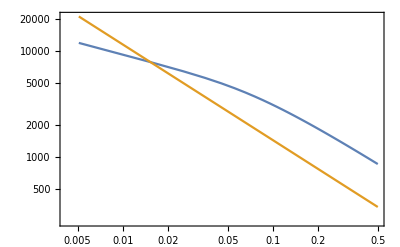

```mathematica
ClearAll[p1,p2,p3,Tc,nc,Hc,X1,Tdg];

Module[{par,Tc,nc,Hc,X1,p1,p2,p3},

par=<|Mbh->MBH, Mdt->0.2MsolYr, α->0.1, OmegaSlope->1.5,R0->0.001PC,xmin->0.0051, xmax->0.5, Nx1-> 50|>;

X1 =  Range[par[xmin],par[xmax],(par[xmax]-par[xmin])/(par[Nx1]-1)];

{Tc,nc,Hc,Tsf}=GetDiskPropsOnGrid[GiveTH,X1,par,KappaStep];

Tdg=(TcGasOnlyDisk[#,par[Mdt],KPE]/.rulForConst/.{M->par[Mbh],α->par[α]})&/@ (PC X1);

p1=MapThread[{#1,#2}&, {X1, Tc}];
p2={};
(*
plt2=MapThread[{#1,#2}&, {X1, Tsf}];
plt2=MapThread[{#1,#2}&,{X1,Tcd[X1]}];
*)

p3=MapThread[{#1,#2}&, {X1, Tdg }];

ListLogLogPlot[{p1,p3}, Joined->True,Frame->True]
]
```

```mathematica
$Path
```

```mathematica
NotebookDirectory[]
```

/Users/dora/WORK/PROGECTS/SCRIPTS_nb/AccretionSolver/

{1.×10^7,1.×10^9}

### dTdzRad, dTdzAdiab plot

```mathematica
pltTgrad[MasIn_:MBH]:=Module[{r,n, MdotRangeInMSolYr,MdotRange,MbhRange,Hgas,T=TSUB, dTAd, dTRad, dT, var,p1,p2,plt={},Tc,nc,Hc,X1(*,Tci,nci,Hci*),TsubIndx,thisPlotSize,dTRadi,dTAdi,par,Ts,xc,imax,MbhRangeLabel},

MbhRangeLabel={"10^7","10^9"};
MbhRange=(ToExpression /@ MbhRangeLabel) Msol;

MdotRangeInMSolYr= {"0.2", "2"};
MdotRange= MsolYr (ToExpression /@ MdotRangeInMSolYr);

par=<|Mdt->0, α->0.1, OmegaSlope->1.5,R0->0.001PC, xmin->0.0051, xmax->0.5, Nx1-> 40 ,Mbh->MasIn|>;

X1 =  Range[par[xmin],par[xmax],(par[xmax]-par[xmin])/(par[Nx1]-1)];

imax=Length[MdotRange];


For[j=1,j≤imax,j++,
par[Mdt]=MdotRange⟦j⟧;

For[k=1,k≤Length[MbhRange],k++,
par[Mbh]=MbhRange⟦k⟧;
Echo[par];

{Tc,nc,Hc,Ts}=GetDiskPropsOnGrid[X1, par,KappaStep]; 
var = MapThread[{#1,#2,#3,#4}&, {nc,Tc, X1 PC, Hc}];
TsubIndx=Position[Tc,_?(#≥TSUB-10 && #≤TSUB+10&)];


{Tci,nci,Hci}= InterpolOnRadGrid[{Tc,nc,Hc}, X1];

xc = Solve[Tci[x]==TSUB,x]⟦1,1,2⟧;

dT=(Convection[#, par,KPDUST ]&)/@var;

dTRad = dT⟦All,1⟧;
dTAd = dT⟦All,2⟧;

dTAd /= Max[Abs[dTRad]]; (* normalize on dTRad *)
dTRad /= Max[Abs[dTRad]];


{dTRadi,dTAdi}=InterpolOnRadGrid[{dTRad,dTAd}, X1];

thisPlotSize=14;
(*Echo[dTAd];Echo[dTRad]; *)

p1= MapThread[{#1,#2}&, {X1, dTRad}];
p2= MapThread[{#1,#2}&, {X1, dTAd}];

AppendTo[plt,
  Plot[{dTRadi[x],dTAdi[x]},{x,par[xmin],par[xmax]},
Frame->True,
AspectRatio->0.5,PlotLabel->"M_BH ="<>MbhRangeLabel⟦k⟧ <>"M_⊙" <> ", Ṁ ="<>MdotRangeInMSolYr⟦j⟧<>"M_⊙yr^-1",
(*PlotLabel->Style["Transition to convection at mid-plane",Black,thisPlotSize],
FrameLabel->{Style["R(pc)",Black,thisPlotSize],Style["T(K)",Black,thisPlotSize]},*)
Filling->{1->{{2},{LightBlue,White}}}]
]


] (* end k-loop *)
]; (* end j-loop *)

plt

(*GraphicsGrid[{plt}, ImageSize->Full]*)

] ;(*end of module*)

plt=(*Quiet@*)pltTgrad[];

plt=GraphicsGrid[Partition[plt,2],ImagePadding->Automatic(*{{Automatic,Automatic},{Automatic,1}}*)
]

(*pltTemp=Rasterize[GraphicsGrid[{{ pltNdens, pltTemp }, {pltPgas, pltPrad}  },ImageSize->Full], ImageResolution->300]
    
FileName    Export["/Users/dora/WORK/PROGECTS/SCRIPTS_nb/AccretionSolver/a_disk_four_pan.pdf", pltTemp]
*)
ClearAll[Tci,nci,Hci]
```

<|Mdt→1.26142×10^25,α→0.1,OmegaSlope→1.5,R0→3.08568×10^15,xmin→0.0051,xmax→0.5,Nx1→40,Mbh→1.989×10^40|>

Part::partw: Part 4 of {0.0051,0.0177897,0.0304795,0.0431692,0.055859,0.0685487,«28»,0.436551,0.449241,0.461931,0.474621,0.48731,0.5}[3.89232×10^43,«9»,KappaStep] does not exist.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 2} and {2, 3} of MapThread[{#1,#2,#3,#4}&,{«1»}]; dimensions are 8 and 40.

Interpolation::innd: First argument in <|Mdt→3.89232×10^43,α→3.08568×10^17,OmegaSlope→4.62852×10^18,R0→9.52141×10^33,xmin→1.5737×10^16,xmax→1.54284×10^18,Nx1→1.23427×10^20,Mbh→6.13741×10^58|> does not contain a list of data and coordinates.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Part::partw: Part 2 of {#1,#2,#3,#4}& does not exist.

Part::partw: Part 3 of {#1,#2,#3,#4}& does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted

GraphicsGrid::list: {} is not a list of lists.

GraphicsGrid::list: GraphicsGrid[{},ImagePadding→Automatic] is not a list of lists.

GraphicsGrid::list: GraphicsGrid[GraphicsGrid[{},ImagePadding→Automatic]] is not a list of lists.

General::stop: Further output of GraphicsGrid::list will be suppressed during this calculation.

GraphicsGrid[GraphicsGrid[GraphicsGrid[{},ImagePadding→Automatic]],ImagePadding→Automatic]

```mathematica
FileName = "/Users/dora/Documents/TEX/torus10/" <> "gradTAdiabVsModTst.pdf";

(*Export[FileName,Rasterize[plt,ImageSize->Full], ImageResolution->300];*)
Export[FileName,plt, ImageResolution->300];
ClearAll[FileName]
```

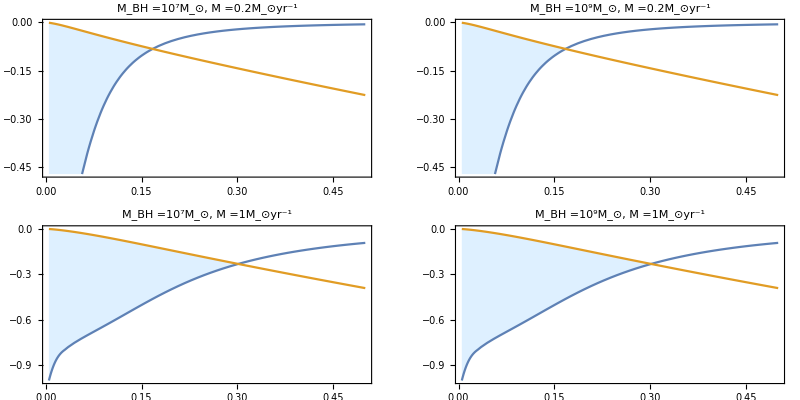

```mathematica
GraphicsGrid[Partition[plt,2],ImagePadding->None(*{{Automatic,Automatic},{Automatic,1}}*)]
```

```mathematica
AppendTo[$Path,"/Users/dora/Library/Mathematica/packages"];
Get["SciDraw`"];
```

DefineStyle::shdw: Symbol DefineStyle appears in multiple contexts {StyleOptions`,Global`}; definitions in context StyleOptions` may shadow or be shadowed by other definitions.

Figure::shdw: Symbol Figure appears in multiple contexts {SciDraw`,Global`}; definitions in context SciDraw` may shadow or be shadowed by other definitions.

CanvasSize::shdw: Symbol CanvasSize appears in multiple contexts {SciDraw`,Global`}; definitions in context SciDraw` may shadow or be shadowed by other definitions.

textit::shdw: Symbol textit appears in multiple contexts {SciDraw`,Global`}; definitions in context SciDraw` may shadow or be shadowed by other definitions.

SetDelayed::write: Tag BoundingRegion in BoundingRegion[ObjectList:{(_Object?(And[«2»]&)|_?(And[«2»]&)|_Object?(And[«2»]&)|_?(And[«2»]&))..}] is Protected.

SetDelayed::write: Tag BoundingRegion in BoundingRegion[obj:_Object?(ObjectExistsQ[Slot[«1»]]&&MemberQ[ClassAncestry[«1»],FigAnchor]&)|_?(ObjectExistsQ[Object[«1»]]&&MemberQ[ClassAncestry[«1»],FigAnchor]&)|_Object?(ObjectExistsQ[Slot[«1»]]&&MemberQ[«1»]&)|_?(ObjectExistsQ[Object[«1»]]&&MemberQ[ClassAncestry[«1»],FigObject]&)] is Protected.

SetDelayed::write: Tag MissingQ in MissingQ[expr_] is Protected.

General::stop: Further output of SetDelayed::write will be suppressed during this calculation.

FigurePanel::shdw: Symbol FigurePanel appears in multiple contexts {SciDraw`,Global`}; definitions in context SciDraw` may shadow or be shadowed by other definitions.

Multipanel::shdw: Symbol Multipanel appears in multiple contexts {SciDraw`,Global`}; definitions in context SciDraw` may shadow or be shadowed by other definitions.

XPlotRange::shdw: Symbol XPlotRange appears in multiple contexts {SciDraw`,Global`}; definitions in context SciDraw` may shadow or be shadowed by other definitions.

YPlotRange::shdw: Symbol YPlotRange appears in multiple contexts {SciDraw`,Global`}; definitions in context SciDraw` may shadow or be shadowed by other definitions.

XExtendRange::shdw: Symbol XExtendRange appears in multiple contexts {SciDraw`,Global`}; definitions in context SciDraw` may shadow or be shadowed by other definitions.

XFrameLabel::shdw: Symbol XFrameLabel appears in multiple contexts {SciDraw`,Global`}; definitions in context SciDraw` may shadow or be shadowed by other definitions.

YFrameLabel::shdw: Symbol YFrameLabel appears in multiple contexts {SciDraw`,Global`}; definitions in context SciDraw` may shadow or be shadowed by other definitions.

XFrameLabelPosition::shdw: Symbol XFrameLabelPosition appears in multiple contexts {SciDraw`,Global`}; definitions in context SciDraw` may shadow or be shadowed by other definitions.

YFrameLabelPosition::shdw: Symbol YFrameLabelPosition appears in multiple contexts {SciDraw`,Global`}; definitions in context SciDraw` may shadow or be shadowed by other definitions.

XPanelGaps::shdw: Symbol XPanelGaps appears in multiple contexts {SciDraw`,Global`}; definitions in context SciDraw` may shadow or be shadowed by other definitions.

𝒮𝒸𝒾𝒟𝓇𝒶𝓌: Publication–quality scientific figures with Mathematica
M. A. Caprio, University of Notre Dame
Version 0.0.7 (March 28, 2015)
View color paletteVisit home page  -Graphics-

```mathematica
pltgrid=Module[{},
   figT= Figure[
Multipanel[
{
	FigurePanel[
	{
	FigGraphics[plt⟦1⟧]
	},
      {1,1},
	XPlotRange-> {0,0.5},
	YPlotRange-> {-1,0}
	];
	FigurePanel[
	 {
          FigGraphics[ plt⟦2⟧ ]
         },
	  {1,2},
	   XPlotRange-> {0,0.5},
	   YPlotRange-> {-1,0}
         ];
	FigurePanel[
	 {
          FigGraphics[ plt⟦3⟧ ]
         },
	  {2,1},
	   XPlotRange-> {0,0.5},
	   YPlotRange-> {-1,0}    
         ];
	FigurePanel[
	 {
          FigGraphics[ plt⟦4⟧ ]
         },
	  {2,2},
	   XPlotRange-> {0,0.5},
	   YPlotRange-> {-1,0}    
         ];
      },
         Dimensions->{2,2},

	XPanelGaps->0.07

         (*FigLabel[{0.5,20},"test",FontSize->20]*)
     ],

CanvasSize->{7,3},
PlotLabel->{"Test",FontSize->14}
(*XFrameLabel->"Excitation quanta"*)
]
] (* emd of mod *)
ClearAll[figT]
```

-Graphics-

```mathematica
Show[pltgrid,ImagePadding->None, PlotLabel->"Test",Frame->True]
```

-Graphics-

# Illuminated gas pressure disk

```mathematica
ClearAll[EqT, EqTsolution, EqS, EqΣsolution, EqTeffsolution, AGasDiskTeffFunc, AGasDiskTempFunc, ADiskΣFunc, Ω, tmp,Eqτc,F0,FlxRul]

EqHoriz = Σ ν -Mdt/(3π) J;
EqVertT = T^4 - 3/(a c) (F0 τc + (4 ϵ)/3 Fn) ;
Eqτc =τc->κ Σ /2;

EqNu = ν -> α  C^2/Ω/.  C^2-> (Rg T/m) ;

(*0 rules *)
OmegaRul = {Ω->G^(1/2) M^(1/2) r^(-3/2)};
FlxRul={F0 -> 3/(8π)Mdt Ω^2};


EqReduced1 = EqHoriz/.EqNu

EqReduced2 = EqVertT/.FlxRul/.Eqτc

EqT =EqReduced2/.Solve[EqReduced1==0,Σ]⟦1⟧//Together//Numerator;
EqT=EqT/.{J->1,m->1};

EqT= EqT/Coefficient[EqT,T,5]//Simplify

%/.rulForConst

(*Solve[EqT==0 && a>0&&c>0&&Fn>0&&ϵ>0,T,Reals]*)

(*
   myCoList[eq_, pat_]:= CoefficientList[eq,pat]
cofs=myCoList[EqT,T]
poRan= Range[0,Length[coLis]-1]
MapThread[(T^#1#2)&,  {poRan,cofs}]
*)
```

-(J Mdt)/(3 π)+(Rg T α Σ)/(m Ω)

T^4-(3 ((4 Fn ϵ)/3+(3 Mdt κ Σ Ω^2)/(16 π)))/(a c)

T^5-(4 Fn T ϵ)/(a c)-(3 Mdt^2 κ Ω^3)/(16 a c π^2 Rg α)

T^5-17638.1 Fn T ϵ-(1.00807×10^-6 Mdt^2 κ Ω^3)/α

## ClearAll[TcGasDiskWithIllum,par,FlxExt,Tc] TcGasDiskWithIllum[r_,Opac_, par_]:= Module[{Mdt=par[Mdt],Hd,rsph,F0, Fn,κ=KPDUST,eq,ρc,Tc, Tsf,μ,coseff}, Fn=par[Alb]par[η](4π CL Gr MBH)/KPE 1/(4π r^2)(*/.rulzGlob*); Fn=par[Alb]par[η] CL^2 Mdt 1/(4π r^2)(*/.rulzGlob*); Hd= 3/(8π)(κ Mdt)/CL; rsph=(r^2+Hd^2)^(1/2); μ=Hd/rsph; coseff=Hd/r; Fn=μ(2μ+1)coseff Fn; eq=T^5-(4 Fn T)/(a c)-(3 Mdt^2 κ Ω^3)/(16 a c π^2 Rg par[α])/.Ω→Omega[r]/.rulForConst; Tc=NSolve[eq==0,T,Reals]//Flatten; (*Print[First[Tc]⟦2⟧];*) (* surface T_s: *) F0=3/(8π)Mdt Omega[r]^2/.rulForConst; Tsf=((F0 + Fn)/SGB)^(1/4)/.Ω→Omega[r]/.rulForConst; (*Print["Fn = ", Fn, " F0 = ", F0, " r=", r/PC, " μ=", μ];*) (*Print["Tsf=",Tsf, " Hd=", Hd];*) ρc=0; {First[Tc]⟦2⟧,Hd,ρc,Tsf} ] ClearAll[p1,p2,p3,Tc,nc,Hc,X1,Tdg,Alb,task]; makePlot[mdot_]:= Module[{par,Tc,Ts,nc,Hc,roc,X1,p1,pltDataList={}, task}, par=<|Mbh→MBH, Mdt→mdot MsolYr, α→0.1, OmegaSlope→1.5,R0→0.001PC,xmin→0.0051, xmax→0.5, Nx1→ 50,η→0.1,Alb→0.50 |>; X1 = Range[par[xmin],par[xmax],(par[xmax]-par[xmin])/(par[Nx1]-1)]; task={0,0.50}; For[i=1,i≤Length[task],i++, par[Alb]=task⟦i⟧; (*Echo@par;*) {Tc,nc,Hc,Ts}=GetDiskPropsOnGrid[TcGasDiskWithIllum,X1,par,KappaStep]; p1=MapThread[{#1,#2}&, {X1, Ts}]; AppendTo[pltDataList, p1] ]; (*make sublimation line*) AppendTo[pltDataList, MapThread[{#1, #2}&, {X1, Table[TSUB, {i, par[Nx1]}]}]]; Module[{thisPlotSize=14,title}, title="T_s with irradiation, "<>" Ṁ = "<>ToString[mdot]<>"M_⊙ yr^-1"; plotDiskTemp =ListLogLogPlot[pltDataList, Joined→True,Frame→True, PlotStyle→{{Thick,Orange}, {Thick,Blue}, {Magenta,Dashed}} ,PlotLabel→Style[title,Black,thisPlotSize], PlotLabels→{"","",Placed[Style["Tsub",thisPlotSize],{Before}(*{0.4,0.1}*)]}, PlotLegends→Placed[LineLegend[{"irradiation OFF" ,"irradiation ON"},LegendFunction→Framed],{0.8,0.87}(*{0.1,0.1}*)], FrameLabel→{Style["R(pc)",Black,thisPlotSize], Style["T(K)",Black,thisPlotSize]} ,ImageSize→Normal ] ] ] plt=GraphicsGrid[{{makePlot[0.2],makePlot[2]}}, Spacings→{-50,0}, ImagePadding→{{Automatic,Automatic},{Automatic,Automatic}}, ImageSize→Full(*72*{8,4}*)] plt=Rasterize[plt, ImageResolution→400,ImageSize→Full] Export["/Users/dora/WORK/PROGECTS/SCRIPTS_nb/AccretionSolver/diskTsurfIluum_1x2pan.pdf", plt ]

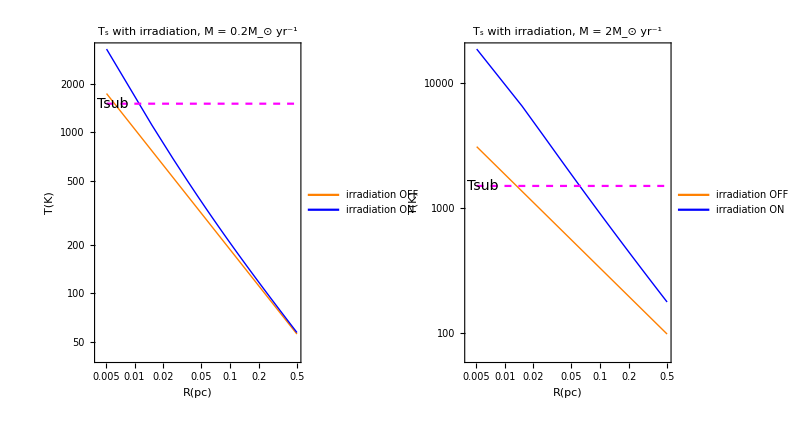

```mathematica
Export["/Users/dora/WORK/PROGECTS/SCRIPTS_nb/AccretionSolver/diskTsurfIluum_1x2pan.pdf",plt,"PDF"]
```

/Users/dora/WORK/PROGECTS/SCRIPTS_nb/AccretionSolver/diskTsurfIluum_1x2pan.pdf

-Graphics-

/Users/dora/WORK/PROGECTS/SCRIPTS_nb/AccretionSolver/diskTsurfIluum_1x2pan.pdf

```mathematica
plt[[2]][[0]]
```

Rule

```mathematica
Figure[
  Multipanel[
{ 
FigurePanel[{FigGraphics[plotDiskTemp]},{1,1}];
	FigurePanel[{FigGraphics[plotDiskTemp]},{1,1}];
 CanvasSize->{7,3},PlotLabel->{"Test",FontSize->14},
XPlotRange-> {0,1},
YPlotRange-> {1,1000}
}
]
]

(*Show[pltgrid]*)
```

-Graphics-

```mathematica
Figure[
Multipanel[
{ 
FigurePanel[{Plot[x^2,{x,0,1}]},{1,1} ];
FigurePanel[{Plot[x^2,{x,0,1}]},,{1,2} ];
},Dimensions->{1,2},XPanelGaps->0.07 
],
CanvasSize->{7,3},PlotLabel->{"Test",FontSize->14},
XPlotRange-> {0,1},
YPlotRange-> {0,1}
(*XFrameLabel->"Excitation quanta"*)
]
```

Figure[Multipanel[{Null},Dimensions→{1,2},XPanelGaps→0.07],CanvasSize→{7,3},PlotLabel→{Test,FontSize→14},XPlotRange→{0,1},YPlotRange→{0,1}]

```mathematica
pltgrid=Module[{},
   figT= Figure[
Multipanel[
{
	FigurePanel[
	{
	FigGraphics[Plot[x^2,{x,0,1}]]
	},
      {1,1},
	XPlotRange-> {0,0.5},
	YPlotRange-> {-1,0}
	];
	FigurePanel[
	 {
          FigGraphics[ Plot[x^2,{x,0,1}] ]
         },
	  {1,2},
	   XPlotRange-> {0,0.5},
	   YPlotRange-> {-1,0}
         ];
	FigurePanel[
	 {
        
	ListPlot[Prime[Range[25]]]
	
         },
	  {2,1},
	   XPlotRange-> {0,1},
	   YPlotRange-> {0,1}    
         ];
	FigurePanel[
	 {
          FigGraphics[ Plot[x^2,{x,0,1}] ]
         },
	  {2,2},
	   XPlotRange-> {0,1},
	   YPlotRange-> {0,1}    
         ];
      },
         Dimensions->{2,2},

	XPanelGaps->0.07

         (*FigLabel[{0.5,20},"test",FontSize->20]*)
     ],

CanvasSize->{7,3},
PlotLabel->{"Test",FontSize->14}
(*XFrameLabel->"Excitation quanta"*)
]
] (* emd of mod *)
ClearAll[figT]
```

-Graphics-

## More on dust sublimation radii

Calculating the ratio of R_AGN  to r_out

```mathematica
ClearAll[M,r1,r0];




Block[{KPDUST=10,rin , rout ,rAgnGal,RadInFun},(*Echo[rg];*)

RadInFun[Mdt_] := (G^(1/3) J^(1/3) M^(1/3) Mdt^(1/3) (3/π)^(1/3))/(2 Tsub^(4/3) σ^(1/3))
(*/.rulForConst/.FilterRules[rulzGlobWithScales,M]/.Tsub->TSUB Subscript[T, 1500]*);




rAgnGal = G M/σ^2;

rul4M={M->Subscript[r, g] CL^2/2};(*Echo[PC/(2Gr MBH/CL^2)];*)

Tc[r_]:= ((3/2)^(1/5) J^(2/5) m^(1/5) mdt^(2/5) κ^(1/5) ((G *M /r^3)^(1/2))^(3/5))/(2 π^(2/5) Rg^(1/5) α^(1/5) σ^(1/5))/.{J->1,m->1,σ->a *c/4};
rin = RadInFun[0.1MsolYr M01];
rout=Assuming[{π>0&& mdt>0&& Rg>0&&M>0&& α>0&& a>0 && c>0 && κ>0 && Ts>0 && G>0},
fullSimplifyReal[Solve[Tc[r]==Ts,r]]
//First]⟦1,2⟧//ReleaseHold;

Print["rout=",(r1/.rulForConst/.rulzGlobWithScales/.{κ->KPDUST Subscript[κ, d],mdt->0.1MsolYr,Ts->1500 Subscript[T, 1500]})/PC];

Block[{rg= 2Gr M/CL^2},
Echo[ PowerExpand[rin/rg]/.FilterRules[rulzGlobWithScales,M]/.{σ->SGB,G->Gr,J->1,Tsub->1500 Subscript[T, 1500]}, "rin = "];

Echo[rg/.FilterRules[rulzGlobWithScales,M],"rg = "];

Echo[(PowerExpand[rAgnGal/rg])/.{σ->100 10^5 Subscript[σ, 100],G->Gr}/.FilterRules[rulzGlobWithScales,M],"rAgnGal ="];

Print["rout/rg = ",(PowerExpand[rout/rg]/.rulForConst/.rulzGlobWithScales/.{κ->KPDUST Subscript[κ, d],mdt->0.1MsolYr Subscript[Mt, 0.1],Ts->1500 Subscript[T, 1500]})//myFormatConvertToNegativePowers];
];

ClearAll[Tc];

r0 = ((ϵ f Mdt c)/(π a Ts^4))^(1/2);

Print["ragn=",(r0/.rulForConst/.rulzGlobWithScales/.{Mdt->0.1MsolYr Subscript[Mt, 0.1],Ts->1500 Subscript[T, 1500]})/PC];

Print["Accretion rate Mdt=", 4Pi CL Gr MBH/KPE/CL^2 η/ϵ/MsolYr/.{ϵ->0.1 Subscript[ϵ, 0.1],η->0.5 Subscript[η, 0.5]}];


res= Assuming[{ϵ>0 && π>0&& Mdt>0 && mdt>0&& Rg>0&&M>0&& a>0&& f>0 && α>0 && c>0 && κ>0&& Ts>0 &&G>0},
(PowerExpand[r0/rout])//Cancel(*fullSimplifyReal*)
]/.rulForConst/.rulzGlobWithScales/.κ->KPDUST Subscript[κ, d]/. Ts->1500 Subscript[T, 1500];
Print["q=r0/rout=",res//myFormatConvertToNegativePowers]

]
Print["Virial Rad Temp = ",MapThread[( (MP #1Gr 10^7 Msol Subscript[M, 7])/(ARAD #2))^(1/4)&, {{10^7 Subscript[n, 7]},{0.1PC Subscript[r, 0.1]}}]];


ClearAll[ϵ, Mdt, mdt, Rg,M, a, f,α,c,κ,Ts,G];
```

rout=3.24078×10^-19 r1

rin =  (5132.98 M01^(1/3))/(M_7^(2/3) T_1500^(4/3))

rg =  2.95222×10^12 M_7

rAgnGal = (4.49378×10^6)/σ_100^2

rout/rg = 149904. Mt_0.1^(4/9) κ_d^(2/9) M_7^(-2/3) T_1500^(-10/9) (α_0.1)^(-2/9)

ragn=0.128476 √((f Mt_0.1 ϵ_0.1)/T_1500^4)

Accretion rate Mdt=(0.110213 η_0.5)/(ϵ_0.1)

q=r0/rout=0.0375355 √f √Mdt α_0.1^(2/9) √(ϵ_0.1) mdt^(-4/9) M_7^(-1/3) T_1500^(-8/9) κ_d^(-2/9)

Virial Rad Temp = {1755.93 ((M_7 n_7)/(r_0.1))^(1/4)}

```mathematica
TcGasOnlyDisk[0.1PC Subscript[r, 0.1],0.1MsolYr,κ]/.rulForConst/.{J->1.,κ->KPE Subscript[κ, e],α->0.1,M->10^7 Msol Subscript[M, 7]}
```

1090.07 (M_7/(r_0.1^3))^(3/10) κ_e^(1/5)

```mathematica
0.02*0.7
```

0.014

```mathematica
10^45/(0.1 CL^2)/MsolYr
```

0.176413

```mathematica
4Pi CL Gr MBH/KPE/CL^2 η/ϵ/MsolYr/.{ϵ->0.1 Subscript[ϵ, 0.1],η->0.5 Subscript[η, 0.5]}
```

(0.110213 η_0.5)/(ϵ_0.1)

```mathematica
ARAD/(3MP)2000^3(RGAS/μ)^-1
```

1.45127×10^11 μ

## q factors plots experiments

```mathematica
MidDiskSubRadRadius[M_,Mdt_] := (G^(1/3) J^(1/3) M^(1/3) Mdt^(1/3) (3/π)^(1/3))/(2 Tsub^(4/3) σ^(1/3));
SurfDiskSubRadRadius
```

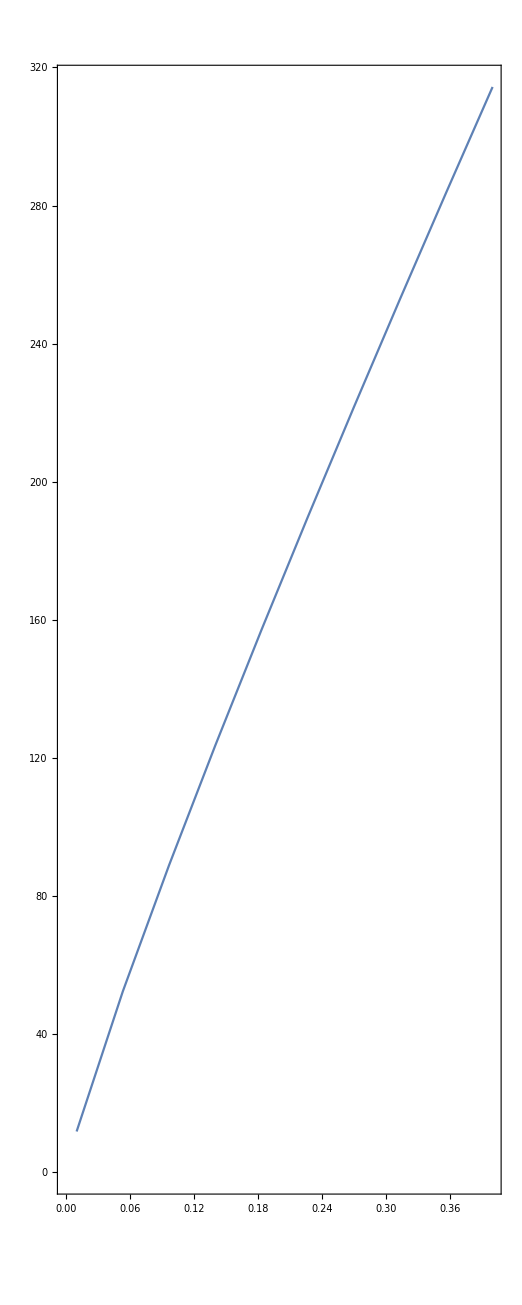

```mathematica
Nmdot=10;
MinMdot = 0.01;
MaxMdot   =0.4;



mdtRange =  Range[MinMdot,MaxMdot ,(MaxMdot-MinMdot)/(Nmdot-1) ];

MdotRange = (FOut[#,par]&)/@ mdtRange;

ToPlot =MapThread[{#1,#2}&, {mdtRange,MdotRange}];


	ListPlot[ ToPlot,Joined->True,Frame->True,AspectRatio->Full]
```

```mathematica
FilterRules[rulzGlobWithScales,M]
```

{M→1.989×10^40 M_7}